```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];SetDirectory[NotebookDirectory[]];
```

## 1. Set up parameters

### 1.1 read input parameters H_0, Ω_b0, Ω_c0, T_CMB, n_s, α, q_0, (Ṽ)_1

```mathematica
inputdata=Import["GR_input_data.txt","Table"]
```

{{70},{0.05},{0.25},{2.7},{1.},{-1.1},{-0.5}}

```mathematica
{inputH0,inputOmb0,inputOmc0,inputTcmb,inputns}={inputdata[[1]][[1]],inputdata[[2]][[1]],inputdata[[3]][[1]],inputdata[[4]][[1]],inputdata[[5]][[1]]};
```

### 1.2 constants and derived quantities

```mathematica
n=4;coord={et,r,th,ph};ccoord={et,x,y,z};
```

```mathematica
mesi=9.1093837015*10^-31;mpsi=1.67262192369*10^-27;mhsi=1.673575*10^-27;Gconsi=6.67430*10^-11;cconsi=299792458;kbconsi=1.380649*10^-23;hconsi=6.62607015*10^-34;econsi=1.602176634*10^-19;ep0consi=8.85418782*10^-12;
```

```mathematica
hbarconsi=hconsi/(2*Pi);alconsi=econsi^2/(4*Pi*ep0consi*hbarconsi*cconsi);hye0si=mesi/(2*hbarconsi^2)*(econsi^2/(4*Pi*ep0consi))^2;sitsi=(8*Pi)/3*(econsi^2/(4*Pi*ep0consi*mesi*cconsi^2))^2;sisbsi=(Pi^2*kbconsi^4)/(60*hbarconsi^3*cconsi^2);
```

```mathematica
megeo=(Gconsi*mesi)/cconsi^2;mpgeo=(Gconsi*mpsi)/cconsi^2;mhgeo=(Gconsi*mhsi)/cconsi^2;sitgeo=sitsi;
```

```mathematica
pgnum1=15;pgnum2=10;pgnum3=8;zeronum=10^-80;errornum1=10^-3;errornum2=10^-2;errornum3=10^-9;
```

```mathematica
H0si=inputH0*1000/(3.08567758128*10^16*10^6);Tcmb=inputTcmb;Omb0num=inputOmb0;Omc0num=inputOmc0;Omga0num=(8*Pi*Gconsi)/(3*H0si^2*cconsi^2)*(8*Pi^5*kbconsi^4)/(15*hconsi^3*cconsi^3)*(Tcmb)^4;Omla0num=1-Omb0num-Omc0num-Omga0num;{Omga0num,Omla0num}
```

{0.0000486065,0.699951}

```mathematica
H0geo=H0si*1/cconsi;menum=megeo*H0geo;mpnum=mpgeo*H0geo;mhnum=mhgeo*H0geo;sitnum=sitsi*H0geo^2
```

3.80922×10^-81

```mathematica
nsnum=inputns;decalrsq=k^(nsnum-1);
```

```mathematica
kanum=8*Pi;H0num=1;{lnaini,lnaend}={-14,0};aininum=N[Exp[lnaini]];numrep0={H0->H0num,ka->kanum,Omb0->Omb0num,Omc0->Omc0num,Omga0->Omga0num,Omla0->Omla0num};
```

## 2. Calculate field equation

### 2.1 curvature quantities

```mathematica
scalarpertfuns={bps[et,x,y,z]->bps[et]*Exp[I*(kx*x+ky*y+kz*z)],bph[et,x,y,z]->bph[et]*Exp[I*(kx*x+ky*y+kz*z)],deugax[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deugay[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deugaz[et,x,y,z]->D[(-3*bth1[et])/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],bpigaxx[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z],bpigayy[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z],bpigazz[et,x,y,z]->2/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,z]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],y,y]-1/3*D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,x],bpigaxy[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,y],bpigaxz[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],x,z],bpigayz[et,x,y,z]->D[(4*(af[et])^2*epga[et]*bth2[et])/(kx^2+ky^2+kz^2)*Exp[I*(kx*x+ky*y+kz*z)],z,y],deepga[et,x,y,z]->4*epga[et]*bth0[et]*Exp[I*(kx*x+ky*y+kz*z)],deubx[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deuby[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deubz[et,x,y,z]->D[vb[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],deepb[et,x,y,z]->epb[et]*deb[et]*Exp[I*(kx*x+ky*y+kz*z)],deucx[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],x],deucy[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],y],deucz[et,x,y,z]->D[vc[et]/(af[et]*Sqrt[kx^2+ky^2+kz^2])*Exp[I*(kx*x+ky*y+kz*z)],z],deepc[et,x,y,z]->epc[et]*dec[et]*Exp[I*(kx*x+ky*y+kz*z)],debt[et,x,y,z]->debt[et]*Exp[I*(kx*x+ky*y+kz*z)],debx[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],x],deby[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],y],debz[et,x,y,z]->D[debs[et]/Sqrt[kx^2+ky^2+kz^2]*Exp[I*(kx*x+ky*y+kz*z)],z]};
```

```mathematica
metric1=(af[et])^2*{{0,0,0,0},{0,1/(1+Omk0*H0^2*r^2),0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};metricet={{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};metricetsph={{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2*(Sin[th])^2}};ctran={et,r*Sin[th]*Cos[ph],r*Sin[th]*Sin[ph],r*Cos[th]};jmet=Table[D[ctran[[i]],coord[[j]]],{i,1,n},{j,1,n}];jmetinv=Simplify[Inverse[jmet]];cmetric1=Simplify[Transpose[jmetinv].metric1.jmetinv/.{Cos[th]->z/r,Sin[th]->Sqrt[x^2+y^2]/r,Cos[ph]->x/Sqrt[x^2+y^2],Sin[ph]->y/Sqrt[x^2+y^2]}/.r->Sqrt[x^2+y^2+z^2]];cmetric=af[et]^2*(1+po*2*bps[et,x,y,z])*{{-1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}+(1-po*2*bph[et,x,y,z])*cmetric1/.Omk0->0/.scalarpertfuns;
```

```mathematica
AbsoluteTiming[poord=1;inversecmetric=Normal[Series[Inverse[cmetric],{po,0,poord}]];chris=Normal[Series[Table[(1/2)*Sum[inversecmetric[[i,s]]*(D[cmetric[[s,k]],ccoord[[j]]]+D[cmetric[[j,s]],ccoord[[k]]]-D[cmetric[[j,k]],ccoord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}],{po,0,poord}]];riemann=Normal[Series[Table[D[chris[[i,j,ll]],ccoord[[k]]]-D[chris[[i,j,k]],ccoord[[ll]]]+Sum[chris[[i,k,s]]*chris[[s,ll,j]]-chris[[i,ll,s]]*chris[[s,k,j]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{ll,1,n}],{po,0,poord}]];ricci=Table[Sum[riemann[[s,j,s,k]],{s,1,n}],{j,1,n},{k,1,n}];riccis=Normal[Series[Sum[inversecmetric[[i,j]]*ricci[[i,j]],{i,1,n},{j,1,n}],{po,0,poord}]];einstein=Normal[Series[Table[ricci[[i,j]]-1/2*cmetric[[i,j]]*riccis,{i,1,n},{j,1,n}],{po,0,poord}]];]
```

{0.080354,Null}

### 2.2 bumblebee contribution

```mathematica
AbsoluteTiming[bdown={af[et]*btf[et],0,0,0}+po*af[et]*{debt[et,x,y,z],debx[et,x,y,z],deby[et,x,y,z],debz[et,x,y,z]}/.scalarpertfuns;bsq=Normal[Series[Sum[inversecmetric[[i,j]]*bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}],{po,0,poord}]];bbdown=Table[bdown[[i]]*bdown[[j]],{i,1,n},{j,1,n}];db=Table[D[bdown[[j]],ccoord[[i]]]-Sum[chris[[s1,i,j]]*bdown[[s1]],{s1,1,n}],{i,1,n},{j,1,n}];bten=Table[db[[i,j]]-db[[j,i]],{i,1,n},{j,1,n}];dbb=Table[D[bbdown[[j,k]],ccoord[[i]]]-Sum[chris[[s1,i,j]]*bbdown[[s1,k]]+chris[[s1,i,k]]*bbdown[[j,s1]],{s1,1,n}],{i,1,n},{j,1,n},{k,1,n}];ddbb=Table[D[dbb[[i2,i3,i4]],ccoord[[i1]]]-Sum[chris[[s1,i1,i2]]*dbb[[s1,i3,i4]]+chris[[s1,i1,i3]]*dbb[[i2,s1,i4]]+chris[[s1,i1,i4]]*dbb[[i2,i3,s1]],{s1,1,n}],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}];tbdown=Normal[Series[Table[xi*(1/2*cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*bbdown[[s1,s2]]*ricci[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-Sum[inversecmetric[[s1,s2]]*bbdown[[i,s1]]*ricci[[j,s2]]+inversecmetric[[s1,s2]]*bbdown[[j,s1]]*ricci[[i,s2]],{s1,1,n},{s2,1,n}]+1/2*(Sum[inversecmetric[[s1,s2]]*ddbb[[s1,i,s2,j]]+inversecmetric[[s1,s2]]*ddbb[[s1,j,s2,i]]-inversecmetric[[s1,s2]]*ddbb[[s1,s2,i,j]],{s1,1,n},{s2,1,n}]-cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*ddbb[[s1,s2,s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]))+ka*(Sum[inversecmetric[[s1,s2]]*bten[[i,s1]]*bten[[j,s2]],{s1,1,n},{s2,1,n}]-1/4*cmetric[[i,j]]*Sum[inversecmetric[[s1,s3]]*inversecmetric[[s2,s4]]*bten[[s1,s2]]*bten[[s3,s4]],{s1,1,n},{s2,1,n},{s3,1,n},{s4,1,n}]-bv*cmetric[[i,j]]+2*bbdown[[i,j]]*bvp)+xi2*(-bsq*einstein[[i,j]]-bdown[[i]]*bdown[[j]]*riccis+Sum[ddbb[[i,j,i1,i2]]*inversecmetric[[i1,i2]],{i1,1,n},{i2,1,n}]-cmetric[[i,j]]*Sum[ddbb[[i1,i2,i3,i4]]*inversecmetric[[i1,i2]]*inversecmetric[[i3,i4]],{i1,1,n},{i2,1,n},{i3,1,n},{i4,1,n}])/.{bv->v1*bsq,bvp->v1},{i,1,n},{j,1,n}],{po,0,poord}]];]
```

{0.422549,Null}

### 2.3 photon energy-momentum tensor

```mathematica
ugaup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deugax[et,x,y,z],deugay[et,x,y,z],deugaz[et,x,y,z]}/.scalarpertfuns;ugadown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ugaup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfgamn=Normal[Series[Table[(ep+p)*ugadown[[i]]*ugadown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epga[et]+po*deepga[et,x,y,z],p->1/3*(epga[et]+po*deepga[et,x,y,z])},{po,0,poord}]]+po*{{0,0,0,0},{0,bpigaxx[et,x,y,z],bpigaxy[et,x,y,z],bpigaxz[et,x,y,z]},{0,bpigaxy[et,x,y,z],bpigayy[et,x,y,z],bpigayz[et,x,y,z]},{0,bpigaxz[et,x,y,z],bpigayz[et,x,y,z],bpigazz[et,x,y,z]}}/.scalarpertfuns;tfgamnup=Normal[Series[Table[Sum[tfgamn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfgamncon=Normal[Series[Table[Sum[D[tfgamnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfgamnup[[i2,i]]+chris[[i,i1,i2]]*tfgamnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.4 baryon energy-momentum tensor

```mathematica
ubup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deubx[et,x,y,z],deuby[et,x,y,z],deubz[et,x,y,z]}/.scalarpertfuns;ubdown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ubup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfbmn=Normal[Series[Table[(ep+p)*ubdown[[i]]*ubdown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epb[et]+po*deepb[et,x,y,z],p->0},{po,0,poord}]]/.scalarpertfuns;tfbmnup=Normal[Series[Table[Sum[tfbmn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfbmncon=Normal[Series[Table[Sum[D[tfbmnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfbmnup[[i2,i]]+chris[[i,i1,i2]]*tfbmnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.5 cold dark matter energy-momentum tensor

```mathematica
ucup={1/af[et],0,0,0}+po*{-1/af[et]*bps[et,x,y,z],deucx[et,x,y,z],deucy[et,x,y,z],deucz[et,x,y,z]}/.scalarpertfuns;ucdown=Normal[Series[Table[Sum[cmetric[[i,i1]]*ucup[[i1]],{i1,1,n}],{i,1,n}],{po,0,poord}]];tfcmn=Normal[Series[Table[(ep+p)*ucdown[[i]]*ucdown[[j]]+p*cmetric[[i,j]],{i,1,n},{j,1,n}]/.{ep->epc[et]+po*deepc[et,x,y,z],p->0},{po,0,poord}]]/.scalarpertfuns;tfcmnup=Normal[Series[Table[Sum[tfcmn[[i1,i2]]*inversecmetric[[i,i1]]*inversecmetric[[j,i2]],{i1,1,n},{i2,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];tfcmncon=Normal[Series[Table[Sum[D[tfcmnup[[i1,i]],ccoord[[i1]]],{i1,1,n}]+Sum[chris[[i1,i1,i2]]*tfcmnup[[i2,i]]+chris[[i,i1,i2]]*tfcmnup[[i1,i2]],{i1,1,n},{i2,1,n}],{i,1,n}],{po,0,poord}]];
```

### 2.6 Einstein field equations

```mathematica
eeq=einstein-ka*tfgamn-ka*tfbmn-ka*tfcmn-tbdown+bla*cmetric/.bla->3 H0^2 Omla0;eequpdown=Normal[Series[Table[Sum[eeq[[i,i1]]*inversecmetric[[i1,j]],{i1,1,n}],{i,1,n},{j,1,n}],{po,0,poord}]];
```

### 2.7 vector field equation

```mathematica
veceq=Normal[Series[Table[Sum[inversecmetric[[s1,s2]]*D[bten[[s2,i]],ccoord[[s1]]],{s1,1,n},{s2,1,n}]-Sum[inversecmetric[[s2,s3]]*(chris[[s1,s2,s3]]*bten[[s1,i]]+chris[[s1,s2,i]]*bten[[s3,s1]]),{s1,1,n},{s2,1,n},{s3,1,n}]+xi/ka*Sum[inversecmetric[[s1,s2]]*bdown[[s1]]*ricci[[s2,i]],{s1,1,n},{s2,1,n}]+xi2/ka*bdown[[i]]*riccis-2*bvp*bdown[[i]]/.{bv->v1*bsq,bvp->v1},{i,1,n}],{po,0,poord}]];
```

### 2.8 Boltzmann equation and conservation equations

```mathematica
boltzeqset={bth0'[et]-(-k bth1[et]+bph'[et]),bth1'[et]-1/3 (k bps[et]+k bth0[et]-3 bga[et] bth1[et]-2 k bth2[et]-bga[et] vb[et]),9/10 bga[et] bth2[et]+1/5 k (-2 bth1[et]+3 bth3[et])+bth2'[et],deb'[et]-(k vb[et]+3 bph'[et]),vb'[et]-1/(3 af[et] epb[et])(-3 k af[et] bps[et] epb[et]-12 af[et] bga[et] bth1[et] epga[et]-4 af[et] bga[et] epga[et] vb[et]-3 epb[et] vb[et] af'[et]),dec'[et]-(k vc[et]+3 bph'[et]),vc'[et]-((-k af[et] bps[et]-vc[et] af'[et])/af[et])};
```

```mathematica
boltzeqhigh=bthl'[et]+k/(2*l+1)*((l+1)*bthlp1[et]-l*bthlm1[et])+bga[et]*(1-KroneckerDelta[l,2]/10)*bthl[et];
```

### 2.9 reduce the field equations and change variable: η→a

```mathematica
{epgasol,epbsol,epcsol}={(3*H0^2*Omga0)/(ka*(af[et])^4),(3*H0^2*Omb0)/(ka*(af[et])^3),(3*H0^2*Omc0)/(ka*(af[et])^3)};{epgasollna,epbsollna,epcsollna}={epgasol,epbsol,epcsol}/.{af[et]->Exp[lna]};{epgapsol,epbpsol,epcpsol}={(-4*af'[et]*epga[et])/af[et],(-3*af'[et]*epb[et])/af[et],(-3*af'[et]*epc[et])/af[et]};
```

```mathematica
grapsol=(√ka af[et]^2 √(epb[et]+epc[et]+epga[et]+3 H0^2/ka*Omla0))/(√3);grappsol=1/6*af[et]^3 (ka*epb[et]+ka*epc[et]+12*H0^2*Omla0);Simplify[eeq/.po->0/.{xi->0,xi2->0,btf[et]->0,btf'[et]->0}/.bla->3*H0^2*Omla0/.{af''[et]->grappsol,af'[et]->grapsol}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
appsol=grappsol;
```

```mathematica
test1=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[eequpdown[[1,1]],po,1]];test2=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/kx*Coefficient[eequpdown[[1,2]],po,1]];test3=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))/(kx*ky)*Coefficient[eequpdown[[2,3]],po,1]];test4=Simplify[ⅇ^(-(ⅈ kx x+ⅈ ky y+ⅈ kz z))*Coefficient[eequpdown[[3,3]],po,1]];{grseleq11,grseleq12,grseleq13,grseleq14}=Simplify[{test1,test2,test3,test4}/.{btf[et]->0,btf'[et]->0,btf''[et]->0}/.{kx->0,ky->k,kz->0},Assumptions->k>0];
```

```mathematica
fieldeqset={grseleq11,grseleq12,grseleq13,grseleq14};
```

```mathematica
ettoa={af''[et]->a*calh[a]*(calh[a]+a*calh'[a]),af'[et]->a*calh[a],af[et]->a,btf[et]->btf[a],btf'[et]->a*calh[a]*btf'[a],btf''[et]->a*calh[a]*(btf''[a]*a*calh[a]+btf'[a]*calh[a]+btf'[a]*a*calh'[a]),bth0[et]->bth0[a],bth0'[et]->a*calh[a]*bth0'[a],bth0''[et]->a*calh[a]*(bth0''[a]*a*calh[a]+bth0'[a]*calh[a]+bth0'[a]*a*calh'[a]),bth1[et]->bth1[a],bth1'[et]->a*calh[a]*bth1'[a],bth1''[et]->a*calh[a]*(bth1''[a]*a*calh[a]+bth1'[a]*calh[a]+bth1'[a]*a*calh'[a]),bth2[et]->bth2[a],bth2'[et]->a*calh[a]*bth2'[a],bth2''[et]->a*calh[a]*(bth2''[a]*a*calh[a]+bth2'[a]*calh[a]+bth2'[a]*a*calh'[a]),bth3[et]->bth3[a],bth3'[et]->a*calh[a]*bth3'[a],bth3''[et]->a*calh[a]*(bth3''[a]*a*calh[a]+bth3'[a]*calh[a]+bth3'[a]*a*calh'[a]),bthl[et]->bthl[a],bthl'[et]->a*calh[a]*bthl'[a],bthlp1[et]->bthlp1[a],bthlm1[et]->bthlm1[a],bph[et]->bph[a],bph[et]->bph[a],bph'[et]->a*calh[a]*bph'[a],bph''[et]->a*calh[a]*(bph''[a]*a*calh[a]+bph'[a]*calh[a]+bph'[a]*a*calh'[a]),bps[et]->bps[a],bps'[et]->a*calh[a]*bps'[a],bps''[et]->a*calh[a]*(bps''[a]*a*calh[a]+bps'[a]*calh[a]+bps'[a]*a*calh'[a]),deb[et]->deb[a],deb'[et]->a*calh[a]*deb'[a],deb''[et]->a*calh[a]*(deb''[a]*a*calh[a]+deb'[a]*calh[a]+deb'[a]*a*calh'[a]),vb[et]->vb[a],vb'[et]->a*calh[a]*vb'[a],vb''[et]->a*calh[a]*(vb''[a]*a*calh[a]+vb'[a]*calh[a]+vb'[a]*a*calh'[a]),dec[et]->dec[a],dec'[et]->a*calh[a]*dec'[a],dec''[et]->a*calh[a]*(dec''[a]*a*calh[a]+dec'[a]*calh[a]+dec'[a]*a*calh'[a]),vc[et]->vc[a],vc'[et]->a*calh[a]*vc'[a],vc''[et]->a*calh[a]*(vc''[a]*a*calh[a]+vc'[a]*calh[a]+vc'[a]*a*calh'[a]),debt[et]->debt[a],debt'[et]->a*calh[a]*debt'[a],debt''[et]->a*calh[a]*(debt''[a]*a*calh[a]+debt'[a]*calh[a]+debt'[a]*a*calh'[a]),debs[et]->debs[a],debs'[et]->a*calh[a]*debs'[a],debs''[et]->a*calh[a]*(debs''[a]*a*calh[a]+debs'[a]*calh[a]+debs'[a]*a*calh'[a]),bga[et]->bga[a]};
```

```mathematica
testeq=af''[et]-appsol/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa;calhsolap=calh'[a]/.Solve[testeq==0,calh'[a]][[1]];
```

```mathematica
fieldeqseta=Simplify[fieldeqset/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa];boltzeqseta=Simplify[boltzeqset/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa];boltzeqhigha=boltzeqhigh/.ettoa;boltzhighsolp=bthl'[a]/.Solve[boltzeqhigha==0,bthl'[a]][[1]]//Simplify;
```

```mathematica
y1set1={bph[a],deb[a],dec[a],vb[a],vc[a],bth0[a],bth1[a],bth2[a]};y1pset1=D[y1set1,a];y2set1={bps[a]};testsol1=Solve[{boltzeqseta[[1]]==0,boltzeqseta[[2]]==0,boltzeqseta[[3]]==0,boltzeqseta[[4]]==0,boltzeqseta[[5]]==0,boltzeqseta[[6]]==0,boltzeqseta[[7]]==0,fieldeqseta[[1]]==0,fieldeqseta[[3]]==0},{bth0'[a],bth1'[a],bth2'[a],deb'[a],dec'[a],vc'[a],vb'[a],bph'[a],bps[a]}];y1psolset1=y1pset1/.testsol1[[1]];y2solset1=y2set1/.testsol1[[1]];
```

```mathematica
y1set=y1set1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};y1pset=D[y1set,a];y2set=y2set1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};y1psolset=y1psolset1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};y2solset=y2solset1/.{bth0[a]->bthf[a,0],bth0'[a]->D[bthf[a,0],a],bth1[a]->bthf[a,1],bth1'[a]->D[bthf[a,1],a],bth2[a]->bthf[a,2],bth2'[a]->D[bthf[a,2],a],bth3[a]->bthf[a,3],bth3'[a]->D[bthf[a,3],a]};
```

```mathematica
AbsoluteTiming[boln=30;boltzhighsolptrset=Simplify[Table[boltzhighsolp/.{l->ll,bthl[a]->bthf[a,ll],bthl'[a]->D[bthf[a,ll],a],bthlm1[a]->bthf[a,ll-1],bthlp1[a]->bthf[a,ll+1]}/.{calh[a]->calhsola}/.{bthf[a,boln+1]->(2*boln+1)/(k*etf[a])*bthf[a,boln]-bthf[a,boln-1]},{ll,1,boln}]];]
```

{0.101113,Null}

```mathematica
fpsoltrset=Join[y1psolset,Table[boltzhighsolptrset[[i]],{i,3,boln}]];ftrset=Join[y1set,Table[bthf[a,i],{i,3,boln}]];fptrset=D[ftrset,a];
```

### 2.10 approximate solution at a→0

```mathematica
testbph=bph0+bph1*a+bph2*a^2+bph3*a^3;testbps=bps0+bps1*a+bps2*a^2+bps3*a^3;testdeb=deb0+deb1*a+deb2*a^2+deb3*a^3;testdec=dec0+dec1*a+dec2*a^2+dec3*a^3;testvb=vb0+vb1*a+vb2*a^2+vb3*a^3;testvc=vc0+vc1*a+vc2*a^2+vc3*a^3;testbth0=bth00+bth01*a+bth02*a^2+bth03*a^3;testbth1=bth10+bth11*a+bth12*a^2+bth13*a^3;testbth2=bth20+bth21*a+bth22*a^2+bth23*a^3;grinisol0={bps0->bph0,bth00->-bph0/2,vb0->0,vc0->0,bth10->0,bth20->0,bth30->0,bth40->0,bth50->0,bth60->0};grinisol1={bph1->-(deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0))/(8 Omga0)+(2 bph0 H0 √Omga0)/(9 bga0),bps1->-(deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0))/(8 Omga0)-(2 bph0 H0 √Omga0)/(3 bga0),deb1->-(3 (deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0)))/(8 Omga0)+(2 bph0 H0 √Omga0)/(3 bga0),dec1->-(3 (deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0)))/(8 Omga0)+(2 bph0 H0 √Omga0)/(3 bga0),vb1->-(bph0 k)/(2 H0 √Omga0),vc1->-(bph0 k)/(2 H0 √Omga0),bth01->-(deb0 Omb0+dec0 Omc0+2 bph0 (Omb0+Omc0))/(8 Omga0)+(2 bph0 H0 √Omga0)/(9 bga0),bth11->(bph0 k)/(6 H0 √Omga0),bth21->0,bth31->0,bth41->0,bth51->0,bth61->0};grinisol2={bph2->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(45 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(405 bga0^2)+1/(240 H0^2 Omga0^2)(21 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+bph0 (42 H0^2 (Omb0+Omc0)^2-8 k^2 Omga0)),bps2->(H0 (25 bph0 (Omb0+Omc0)+8 (deb0 Omb0+dec0 Omc0)))/(45 bga0 √Omga0)+(32 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(405 bga0^2)+1/(240 H0^2 Omga0^2)(21 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+bph0 (42 H0^2 (Omb0+Omc0)^2-8 k^2 Omga0)),deb2->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(15 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(135 bga0^2)+1/(80 H0^2 Omga0^2)7 (3 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+2 bph0 (3 H0^2 (Omb0+Omc0)^2-2 k^2 Omga0)),dec2->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(15 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(135 bga0^2)+1/(80 H0^2 Omga0^2)7 (3 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+2 bph0 (3 H0^2 (Omb0+Omc0)^2-2 k^2 Omga0)),vb2->(2 bph0 k)/(9 bga0)+(k (deb0 Omb0+dec0 Omc0+3 bph0 (Omb0+Omc0)))/(8 H0 Omga0^(3/2)),vc2->(2 bph0 k)/(9 bga0)+(k (deb0 Omb0+dec0 Omc0+6 bph0 (Omb0+Omc0)))/(24 H0 Omga0^(3/2)),bth02->-(H0 (5 bph0 (Omb0+Omc0)+2 (deb0 Omb0+dec0 Omc0)))/(45 bga0 √Omga0)-(8 bph0 H0 (9 bga1+34 H0 √Omga0) √Omga0)/(405 bga0^2)+1/(240 H0^2 Omga0^2)7 (3 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+2 bph0 (3 H0^2 (Omb0+Omc0)^2-2 k^2 Omga0)),bth12->-(2 bph0 k)/(27 bga0)-(k (deb0 Omb0+dec0 Omc0+3 bph0 (Omb0+Omc0)))/(24 H0 Omga0^(3/2)),bth22->0,bth32->0,bth42->0,bth52->0,bth62->0};grinisol3={bph3->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-172 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-158 k^2 Omga0)+(deb0 Omb0+dec0 Omc0) (567 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(77760 bga0^3 H0^2 Omga0^3),bps3->-((192 bga0 H0^3 Omga0^(5/2) (231 bga1 bph0 (Omb0+Omc0)+75 bga1 (deb0 Omb0+dec0 Omc0)+656 bph0 H0 (Omb0+Omc0) √Omga0+360 H0 (deb0 Omb0+dec0 Omc0) √Omga0-300 bga2 bph0 Omga0)+1280 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (66 Omb0+41 Omc0) (deb0 Omb0+dec0 Omc0)+675 bph0 H0^2 (4 Omb0^2+7 Omb0 Omc0+3 Omc0^2)-260 bph0 k^2 Omga0)+9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-158 k^2 Omga0)+(deb0 Omb0+dec0 Omc0) (567 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(77760 bga0^3 H0^2 Omga0^3)),deb3->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-52 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-458 k^2 Omga0)+7 (deb0 Omb0+dec0 Omc0) (81 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(25920 bga0^3 H0^2 Omga0^3),dec3->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-52 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-398 k^2 Omga0)+3 (deb0 Omb0+dec0 Omc0) (189 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(25920 bga0^3 H0^2 Omga0^3),vb3->-(8 bph0 k (9 bga1+34 H0 √Omga0))/(405 bga0^2)-(2 k (deb0 Omb0+dec0 Omc0+5 bph0 (Omb0+Omc0)))/(45 bga0 Omga0)-1/(160 H0^3 Omga0^(5/2))k (2 H0^2 (13 Omb0+8 Omc0) (deb0 Omb0+dec0 Omc0)+bph0 H0^2 (57 Omb0^2+99 Omb0 Omc0+42 Omc0^2)-8 bph0 k^2 Omga0),vc3->-(8 bph0 k (9 bga1+34 H0 √Omga0))/(405 bga0^2)-(2 k (deb0 Omb0+dec0 Omc0+5 bph0 (Omb0+Omc0)))/(45 bga0 Omga0)-1/(480 H0^3 Omga0^(5/2))k (18 H0^2 (Omb0+Omc0) (deb0 Omb0+dec0 Omc0)+bph0 (81 H0^2 (Omb0+Omc0)^2-4 k^2 Omga0)),bth03->(192 bga0 H0^3 Omga0^(5/2) (39 bga1 bph0 (Omb0+Omc0)+15 bga1 (deb0 Omb0+dec0 Omc0)+104 bph0 H0 (Omb0+Omc0) √Omga0+72 H0 (deb0 Omb0+dec0 Omc0) √Omga0-60 bga2 bph0 Omga0)+256 bph0 H0^3 Omga0^(7/2) (45 bga1^2+386 bga1 H0 √Omga0+816 H0^2 Omga0)+16 bga0^2 H0 Omga0^(3/2) (18 H0^2 (12 Omb0+7 Omc0) (deb0 Omb0+dec0 Omc0)+27 bph0 H0^2 (14 Omb0^2+23 Omb0 Omc0+9 Omc0^2)-52 bph0 k^2 Omga0)-9 bga0^3 (2 bph0 (Omb0+Omc0) (567 H0^2 (Omb0+Omc0)^2-458 k^2 Omga0)+7 (deb0 Omb0+dec0 Omc0) (81 H0^2 (Omb0+Omc0)^2-20 k^2 Omga0)))/(77760 bga0^3 H0^2 Omga0^3),bth13->1/38880 k ((256 bph0 (9 bga1+34 H0 √Omga0))/bga0^2+(576 (deb0 Omb0+dec0 Omc0+5 bph0 (Omb0+Omc0)))/(bga0 Omga0)+1/(H0^3 Omga0^(5/2))81 (2 H0^2 (13 Omb0+8 Omc0) (deb0 Omb0+dec0 Omc0)+bph0 H0^2 (57 Omb0^2+99 Omb0 Omc0+42 Omc0^2)-8 bph0 k^2 Omga0)),bth23->(2 bph0 k^2)/(27 bga0 H0 √Omga0),bth33->0,bth43->0,bth53->0,bth63->0};
```

```mathematica
adbcon={deb0->3*bth00,dec0->3*bth00};gradbcon=adbcon/.grinisol0
```

{deb0→-(3 bph0)/2,dec0→-(3 bph0)/2}

## 3. Solve the background equations numerically

```mathematica
grapsola=Simplify[grapsol/.{epga[et]->epgasol,epb[et]->epbsol,epc[et]->epcsol}/.ettoa,Assumptions->{ka>0,a>0,H0>0}];grcalhsola=Simplify[grapsola/a,Assumptions->{a>0,ka>0,H0>0}];calhsola=grcalhsola;calhsollna=calhsola/.a->Exp[lna];
```

```mathematica
{appsolnum,btpsolnum,calhsolanum}={appsol,btpsol,calhsola}/.{epb[et]->epbsol,epc[et]->epcsol,epga[et]->epgasol}/.numrep0;
```

```mathematica
tend=NIntegrate[1/calhsolanum,{a,0,1}];etend=NIntegrate[1/(calhsolanum*a),{a,0,1}];etininum1=NIntegrate[1/(calhsolanum*a),{a,0,Exp[lnaini-0.1]}];btendnum=3.6;bumbgsolb=NDSolve[{appsolnum==af''[et],tf'[et]==af[et],af[etend]==1,af'[etend]==1,tf[etend]==tend},{af,tf},{et,etend,0},PrecisionGoal->pgnum1];
```

```mathematica
bgsol=bumbgsolb;testa=af/.bumbgsolb[[1]];{etnum1,etnum2}=testa["Domain"][[1]];{anum1,anum2}={af[et]/.bumbgsolb[[1]]/.et->etnum1,af[et]/.bumbgsolb[[1]]/.et->etnum2};Print[{Log[af[et]],btf[et],tf[et]}/.bumbgsolb[[1]]/.et->etininum1]
```

{-14.1494,btf[0.000107795],4.22232×10^-8}

```mathematica
solnpt=5000;etset=Table[Exp[Log[etininum1]+(Log[etnum2]-Log[etininum1])*(i-1)/(solnpt-1)],{i,1,solnpt}];soltab=Table[If[etset[[i]]<=etend,{Log[af[et]],af'[et]/af[et],btf[et]}/.bumbgsolb[[1]]/.et->etset[[i]],{Log[af[et]],af'[et]/af[et],btf[et]}/.bumbgsolf[[1]]/.et->etset[[i]]],{i,1,solnpt}];soltab[[-1,1]]=0;bumcalhfitlna=Interpolation[Table[{soltab[[i,1]],soltab[[i,2]]},{i,1,solnpt}]];bumbtfitlna=Interpolation[Table[{soltab[[i,1]],soltab[[i,3]]},{i,1,solnpt}]];bumetfitlna=Interpolation[Table[{soltab[[i,1]],etset[[i]]},{i,1,solnpt}]];calhfitlna=bumcalhfitlna;btfitlna=bumbtfitlna;etfitlna=bumetfitlna;
```

## 4. Solve X_e

```mathematica
Trapezoidnintg[xlist_,ylist_]:=Module[{sum=0},sum=Sum[1/2*(ylist[[i]]+ylist[[i+1]])*(xlist[[i+1]]-xlist[[i]]),{i,1,Length[xlist]-1}];sum];Simpsonnintg[xlist_,ylist_]:=Module[{sum=0},If[OddQ[Length[xlist]],sum=Sum[-(((xlist⟦i⟧-xlist⟦2+i⟧) (xlist⟦2+i⟧^2 (-ylist⟦i⟧+ylist⟦1+i⟧)+xlist⟦i⟧^2 (ylist⟦1+i⟧-ylist⟦2+i⟧)-3 xlist⟦1+i⟧^2 (ylist⟦i⟧+ylist⟦2+i⟧)+2 xlist⟦1+i⟧ xlist⟦2+i⟧ (2 ylist⟦i⟧+ylist⟦2+i⟧)-2 xlist⟦i⟧ xlist⟦2+i⟧ (ylist⟦i⟧+ylist⟦1+i⟧+ylist⟦2+i⟧)+2 xlist⟦i⟧ xlist⟦1+i⟧ (ylist⟦i⟧+2 ylist⟦2+i⟧)))/(6 (xlist⟦i⟧-xlist⟦1+i⟧) (xlist⟦1+i⟧-xlist⟦2+i⟧))),{i,1,Length[xlist]-2,2}],Print["Warning: Number of intervals are odd"]];sum];
```

```mathematica
numrepbxe={bla2s1s->8.227,be1->-hye0si,me->mesi,mh->mhsi,al->alconsi,hbar->hbarconsi,c->cconsi,ka->8*(Pi*Gconsi)/cconsi^2,kb->kbconsi,sit->sitsi,sisb->sisbsi,hye0->hye0si,H0->H0si,Omb0->Omb0num,Omga0->Omga0num};
```

```mathematica
{sahaeqlhs,sahaeqrhs}={bxe^2/(1-bxe),1/nb*((me*kb*btb)/(2*Pi*hbar^2))^(3/2)*Exp[be1/(kb*btb)]};sahaeqrhs1=Simplify[sahaeqrhs/.nb->epb/(mh*c^2)/.btb->((c*epga)/(4*sisb))^(1/4)/.{epb->epbsol,epga->epgasol},Assumptions->af[et]>0];sahaeqrhs1num=sahaeqrhs1/.numrepbxe;
```

```mathematica
{bxecut1num,bxecut2num}={1-errornum3,0.99};test=sahaeqrhs1num/.af[et]->Exp[lna];test1=sahaeqlhs/.bxe->bxecut1num;test2=sahaeqlhs/.bxe->bxecut2num;lnabxecut1=lna/.FindRoot[test==test1,{lna,-8}][[1]];lnabxecut2=lna/.FindRoot[test==test2,{lna,-8}][[1]];testnpt=100;testdelta=0.0001;testlnaset=Reverse[Table[lnabxecut2-Exp[Log[testdelta]+(Log[lnabxecut2-lnabxecut1]-Log[testdelta])/(testnpt-1)*(i-1)],{i,1,testnpt}]];testrhsset=Table[sahaeqrhs1num/.af[et]->Exp[testlnaset[[i]]],{i,1,testnpt}];testbxeset=Table[1/2 (-rhs+√rhs √(4+rhs))/.rhs->testrhsset[[i]],{i,1,testnpt}];testbxefit=Interpolation[Table[{testlnaset[[i]],testbxeset[[i]]},{i,1,testnpt}],InterpolationOrder->3,Method->"Spline"];
```

```mathematica
(* Peebles equation *)
```

```mathematica
bxebtbplna={a/calh*bcr*(be*(1-bxe)-nbh*al2*bxe^2),-2*btb+c/calh*8/3*mu/me*epga/epb*a*ne*sit*(btga-btb)};
```

```mathematica
bxebtbplnaeqset=Simplify[bxebtbplna/.{bcr->(blaal+bla2s1s)/(blaal+bla2s1s+be*Exp[3 hye0/(4kb*btb)])}/.blaal->1/(Pi^2*n1s)*((3*hye0)/(4*hbar*c))^3*calh/a/.{be->((me*kb*btb)/(2*Pi*hbar^2))^(3/2)*Exp[-hye0/(kb*btb)]*al2}/.al2->(64*Pi)/Sqrt[27*Pi]*(al^2*hbar^2)/(me^2*c)*Sqrt[hye0/(kb*btb)]*0.448*Log[hye0/(kb*btb)]/.{n1s->(1-bxe)*nbh,ne->bxe*nbh}/.nbh->epb/(mh*c^2)/.{btga->((c*epga)/(4*sisb))^(1/4)}/.{epb->epbsol,epga->epgasol}/.{mu->mh/(1+bxe)}/.af[et]->a,Assumptions->a>0];
```

```mathematica
bxebtbplnaeqsetnum=bxebtbplnaeqset/.numrepbxe/.calh->H0si*calhfitlna[lna]/.a->Exp[lna]/.{bxe->bxe[lna],btb->btb[lna]};bxesol=NDSolve[{bxebtbplnaeqsetnum[[1]]==bxe'[lna],bxebtbplnaeqsetnum[[2]]==btb'[lna],bxe[testlnaset[[-1]]]==testbxeset[[-1]],btb[testlnaset[[-1]]]==Tcmb/Exp[testlnaset[[-1]]]},{bxe,btb},{lna,testlnaset[[-1]],0}];
```

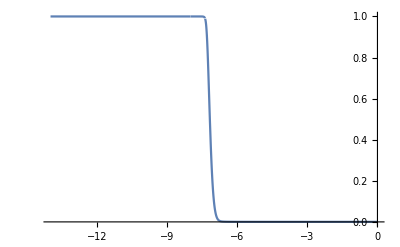

```mathematica
bxeflna=Piecewise[{{1,lna<testlnaset[[1]]},{testbxefit[lna],testlnaset[[1]]<=lna<=testlnaset[[-1]]},{bxe[lna]/.bxesol[[1]],lna>testlnaset[[-1]]}}];bxelna[lna_]=bxeflna;bganum=Exp[lna]*bxeflna*epbsollna/mhnum*sitnum/.numrep0;Plot[bxeflna,{lna,lnaini,0}]
```

```mathematica
AbsoluteTiming[npt1=1000;xsettemp=Table[lnaini+(lnaend-lnaini)/(npt1-1)*(i-1),{i,1,npt1}];ysettemp=Table[0,{i,1,npt1}];lnanpttemp=131;Do[{lna1temp,lna2temp}={xsettemp[[npt1-i]],xsettemp[[npt1-i+1]]};lnasettemp=Table[lna1temp+(lna2temp-lna1temp)/(lnanpttemp-1)*(ii-1),{ii,1,lnanpttemp}];bgasettemp=Table[bganum/calhfitlna[lna]/.lna->lnasettemp[[ii]],{ii,1,lnanpttemp}];intgtemp=Simpsonnintg[lnasettemp,bgasettemp];ysettemp[[npt1-i]]=ysettemp[[npt1-i+1]]+intgtemp,{i,1,npt1-1}]]
```

{3.13693,Null}

```mathematica
taunum=Interpolation[Table[{xsettemp[[i]],ysettemp[[i]]},{i,1,npt1}],InterpolationOrder->3,Method->"Spline"];gnum=bganum*Exp[-taunum[lna]];
```

## 5. Solve the perturbation equations numerically

```mathematica
{knummin,knummax}={0.01,1500};kcoanpt=200;knumcoaset=Table[knummin+(knummax-knummin)*(i-1)^2/(kcoanpt-1)^2,{i,1,kcoanpt}];(* knumcoaset=Table[knummin+(knummax-knummin)/(kcoanpt-1)*(i-1),{i,1,kcoanpt}]; *)lnacoanpt=1000;lna1num=-8.5;lnacoaset=Table[lna1num+(lnaend-lna1num)*(i-1)/(lnacoanpt-1),{i,1,lnacoanpt}];kpauseset={0,IntegerPart[7*kcoanpt/25],IntegerPart[11*kcoanpt/25],IntegerPart[15*kcoanpt/25],IntegerPart[19*kcoanpt/25],IntegerPart[22*kcoanpt/25],kcoanpt}
```

{0,56,88,120,152,176,200}

```mathematica
kpauseind=1;If[kpauseind==1,Export[StringJoin["GR_background_data.txt"],Table[{etset[[i]],soltab[[i,1]],soltab[[i,2]],soltab[[i,3]]},{i,1,Length[etset]}],"Table"];Export[StringJoin["GR_lna_data.txt"],lnacoaset,"Table"];Export[StringJoin["GR_k_data.txt"],knumcoaset,"Table"];]
```

```mathematica
labelsep=1;sourcedis1set=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];sourcedis2set=Table[0,{i,1,lnacoanpt},{j,1,kcoanpt}];
```

```mathematica
labelsol=0;If[labelsol==0,{parbth00,parc1,parc4}={1,0,0}];If[labelsol==1,{parbth00,parc1,parc4}={0,1,0}];If[labelsol==4,{parbth00,parc1,parc4}={0,0,1}]
```

```mathematica
AbsoluteTiming[Do[knum=knumcoaset[[kcoai]];{bth00num,solc1,solc4}={parbth00,parc1,parc4}*Sqrt[decalrsq]/.k->knum;finiset={testbph,testdeb,testdec,testvb,testvc}/.grinisol3/.grinisol2/.grinisol1/.grinisol0/.gradbcon/.numrep0/.bph0->-2*bth00num/.{bga0->bxeflna*(3*Omb0num)/(8*Pi*mhnum)*sitnum,bga1->0,bga2->0}/.k->knum/.lna->lnaini/.a->aininum;bthiniset={testbth0,testbth1,testbth2}/.grinisol3/.grinisol2/.grinisol1/.grinisol0/.gradbcon/.numrep0/.bph0->-2*bth00num/.{bga0->bxeflna*(3*Omb0num)/(8*Pi*mhnum)*sitnum,bga1->0,bga2->0}/.k->knum/.lna->lnaini/.a->aininum;If[labelsep==0,Print[{kcoai,knum}];fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];{source1f1,source1f2}={gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a]),-gnum*vb[a]}/.numrep0/.lna->Log[a]/.bumsol[[1]]];If[labelsep==1,etininum=bumetfitlna[Log[aininum]];asep1=1;parnum=1.8;If[parnum*boln/knum>=etend,Print["1 ",{kcoai,knum,parnum*boln/knum,etend}];fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];{source1f1,source1f2}={gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a]),-gnum*vb[a]}/.numrep0/.lna->Log[a]/.bumsol[[1]]];If[etininum<parnum*boln/knum<etend,Print["2 ",{kcoai,knum,parnum*boln/knum,etend}];asep1=af[et]/.bgsol[[1]]/.et->parnum*boln/knum;fpsoltrsetnum=fpsoltrset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;y2solsetnum=y2solset/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum;ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,Length[fpsoltrset]}]];ndsoliniset=Join[{bph[aininum]==finiset[[1]],deb[aininum]==finiset[[2]],dec[aininum]==finiset[[3]],vb[aininum]==finiset[[4]],vc[aininum]==finiset[[5]],bthf[aininum,0]==bthiniset[[1]],bthf[aininum,1]==bthiniset[[2]],bthf[aininum,2]==bthiniset[[3]]},Table[bthf[aininum,i]==0,{i,3,boln}]];ndsolfset=Join[{bph,bps,deb,dec,vb,vc,bthf[a,0]},Table[bthf[a,i],{i,1,boln}]];bumsol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,aininum,asep1},AccuracyGoal->pgnum3,"StartingStepSize"->10^-pgnum1];fsep1set={bph[a],deb[a],dec[a],vb[a],vc[a],bthf[a,0],bthf[a,1],bthf[a,2]}/.bumsol[[1]]/.a->asep1;sep1eqnumber=8;fpsoltrsetnum=Table[fpsoltrset[[i]]/.{bthf[a,3]->5/(k*etf[a])*bthf[a,2]-bthf[a,1]}/.{calh[a]->calhsola,btf[a]->bumbtfitlna[lna],bga[a]->bganum,etf[a]->bumetfitlna[lna]}/.lna->Log[a]/.numrep0/.k->knum,{i,1,sep1eqnumber}];ndsoleqset=Join[Table[y2set[[i]]==y2solsetnum[[i]],{i,1,Length[y2set]}],Table[fptrset[[i]]==fpsoltrsetnum[[i]],{i,1,sep1eqnumber}]];ndsoliniset={bph[asep1]==fsep1set[[1]],deb[asep1]==fsep1set[[2]],dec[asep1]==fsep1set[[3]],vb[asep1]==fsep1set[[4]],vc[asep1]==fsep1set[[5]],bthf[asep1,0]==fsep1set[[6]],bthf[asep1,1]==fsep1set[[7]],bthf[asep1,2]==fsep1set[[8]]};ndsolfset={bph,bps,deb,dec,vb,vc,bthf[a,0],bthf[a,1],bthf[a,2]};bumsep1sol=NDSolve[{ndsoleqset,ndsoliniset},ndsolfset,{a,asep1,1},PrecisionGoal->pgnum3,"StartingStepSize"->10^-pgnum3];source1f1=Piecewise[{{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.lna->Log[a]/.bumsol[[1]],a<asep1},{gnum*(bthf[a,0]+bps[a])+Exp[-taunum[lna]]*a*calhsola*(bph'[a]+bps'[a])/.numrep0/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}];source1f2=Piecewise[{{-gnum*vb[a]/.numrep0/.lna->Log[a]/.bumsol[[1]],a<asep1},{-gnum*vb[a]/.numrep0/.lna->Log[a]/.bumsep1sol[[1]],a>=asep1}}]]];Do[{sourcedis1set[[lnai,kcoai]],sourcedis2set[[lnai,kcoai]]}={source1f1,source1f2}/.a->Exp[lnacoaset[[lnai]]],{lnai,1,lnacoanpt}],{kcoai,1,kcoanpt}]]
```

{1,0.01}

General::munfl: Exp[-710.169] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{2,0.0478776}

{3,0.16151}

{4,0.350898}

{5,0.616041}

{6,0.956939}

{7,1.37359}

{8,1.866}

{9,2.43417}

{10,3.07808}

{11,3.79776}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{12,4.59319}

{13,5.46437}

{14,6.41131}

{15,7.43401}

{16,8.53246}

{17,9.70666}

{18,10.9566}

{19,12.2823}

{20,13.6838}

{21,15.161}

{22,16.714}

{23,18.3427}

{24,20.0472}

{25,21.8275}

{26,23.6835}

{27,25.6152}

{28,27.6228}

{29,29.706}

{30,31.865}

{31,34.0998}

{32,36.4104}

{33,38.7966}

{34,41.2587}

{35,43.7965}

{36,46.41}

{37,49.0993}

{38,51.8644}

{39,54.7052}

{40,57.6218}

{41,60.6141}

{42,63.6822}

{43,66.826}

{44,70.0456}

{45,73.341}

{46,76.7121}

{47,80.159}

{48,83.6816}

{49,87.2799}

{50,90.9541}

{51,94.7039}

{52,98.5296}

{53,102.431}

{54,106.408}

{55,110.461}

{56,114.59}

{57,118.794}

{58,123.074}

{59,127.43}

{60,131.862}

{61,136.369}

{62,140.952}

{63,145.611}

{64,150.346}

{65,155.157}

{66,160.043}

{67,165.005}

{68,170.042}

{69,175.156}

{70,180.345}

{71,185.61}

{72,190.951}

{73,196.367}

{74,201.86}

{75,207.428}

{76,213.071}

{77,218.791}

{78,224.586}

{79,230.457}

{80,236.404}

{81,242.427}

{82,248.525}

{83,254.699}

{84,260.949}

{85,267.274}

{86,273.676}

{87,280.153}

{88,286.705}

{89,293.334}

{90,300.038}

{91,306.818}

{92,313.674}

{93,320.606}

{94,327.613}

{95,334.696}

{96,341.855}

{97,349.09}

{98,356.4}

{99,363.786}

{100,371.248}

{101,378.786}

{102,386.399}

{103,394.088}

{104,401.853}

{105,409.694}

{106,417.61}

{107,425.602}

{108,433.67}

{109,441.814}

{110,450.034}

{111,458.329}

{112,466.7}

{113,475.146}

{114,483.669}

{115,492.267}

{116,500.941}

{117,509.691}

{118,518.516}

{119,527.417}

{120,536.394}

{121,545.447}

{122,554.576}

{123,563.78}

{124,573.06}

{125,582.416}

{126,591.847}

{127,601.354}

{128,610.937}

{129,620.596}

{130,630.331}

{131,640.141}

{132,650.027}

{133,659.989}

{134,670.026}

{135,680.14}

{136,690.329}

{137,700.594}

{138,710.934}

{139,721.351}

{140,731.843}

{141,742.411}

{142,753.054}

{143,763.773}

{144,774.569}

{145,785.439}

{146,796.386}

{147,807.408}

{148,818.507}

{149,829.68}

{150,840.93}

{151,852.256}

{152,863.657}

{153,875.134}

{154,886.686}

{155,898.315}

{156,910.019}

{157,921.799}

{158,933.654}

{159,945.586}

{160,957.593}

{161,969.676}

{162,981.835}

{163,994.069}

{164,1006.38}

{165,1018.77}

{166,1031.23}

{167,1043.76}

{168,1056.38}

{169,1069.07}

{170,1081.83}

{171,1094.67}

{172,1107.59}

{173,1120.58}

{174,1133.65}

{175,1146.79}

{176,1160.01}

{177,1173.31}

{178,1186.68}

{179,1200.12}

{180,1213.65}

{181,1227.24}

{182,1240.92}

{183,1254.67}

{184,1268.49}

{185,1282.39}

{186,1296.37}

{187,1310.42}

{188,1324.55}

{189,1338.76}

{190,1353.03}

{191,1367.39}

{192,1381.82}

{193,1396.33}

{194,1410.91}

{195,1425.57}

{196,1440.3}

{197,1455.12}

{198,1470.}

{199,1484.96}

{200,1500.}

{422.15,Null}

```mathematica
AbsoluteTiming[Export[StringJoin["GR_sourcedis1set_data.txt"],sourcedis1set,"Table"];Export[StringJoin["GR_sourcedis2set_data.txt"],sourcedis2set,"Table"];]
```

{1.53136,Null}

## 6. Print total time used

```mathematica
Print["End: ",TimeUsed[]]
```

End: 951.312